```mathematica
Quiet@Remove["`*"]
```

```mathematica
SetOptions[SelectedNotebook[],PrintingStyleEnvironment->"Printout",ShowSyntaxStyles->True]
```

```mathematica
mM=LinguisticAssistant
```

7.346×10^22

```mathematica
mE=LinguisticAssistant
```

5.9721986×10^24

## Lagrange point

```mathematica
Solve[M1/(R-r)^2==M2/r^2+(M1/(M1+M2)R-r)((M1+M2)/R^3),r]
```

{{r→Root[-M2 R^5+2 M2 R^4 #1-M2 R^3 #1^2+(3 M1 R^2+M2 R^2) #1^3+(-3 M1 R-2 M2 R) #1^4+(M1+M2) #1^5&,1]},{r→Root[-M2 R^5+2 M2 R^4 #1-M2 R^3 #1^2+(3 M1 R^2+M2 R^2) #1^3+(-3 M1 R-2 M2 R) #1^4+(M1+M2) #1^5&,2]},{r→Root[-M2 R^5+2 M2 R^4 #1-M2 R^3 #1^2+(3 M1 R^2+M2 R^2) #1^3+(-3 M1 R-2 M2 R) #1^4+(M1+M2) #1^5&,3]},{r→Root[-M2 R^5+2 M2 R^4 #1-M2 R^3 #1^2+(3 M1 R^2+M2 R^2) #1^3+(-3 M1 R-2 M2 R) #1^4+(M1+M2) #1^5&,4]},{r→Root[-M2 R^5+2 M2 R^4 #1-M2 R^3 #1^2+(3 M1 R^2+M2 R^2) #1^3+(-3 M1 R-2 M2 R) #1^4+(M1+M2) #1^5&,5]}}

### M2 << M1 or mM << mE

```mathematica
Roots
```

Roots

```mathematica
L1=(mM/(3mE))^(1/3)
```

0.16005

## Hamiltonian contourplot in x,y

```mathematica
H=(px^2+py^2)/(2m3)+px*y-py*x-α((1-q)/(√((x+q)^2+y^2))+q/(√((1-q-x)^2+y^2)))
```

(px^2+py^2)/(2 m3)-py x+px y-(q/(√((1-q-x)^2+y^2))+(1-q)/(√((q+x)^2+y^2))) α

```mathematica
rules={
px->0.3,
py->0.3,
m3->1,
α->1,
q->0.012
};
```

```mathematica
H/.rules
```

0.09-0.3 x+0.3 y-0.012/(√((0.988-x)^2+y^2))-0.988/(√((0.012+x)^2+y^2))

```mathematica
H/.rules
```

0.09-0.3 x+0.3 y-0.012/(√((0.988-x)^2+y^2))-0.988/(√((0.012+x)^2+y^2))

```mathematica
0.020000000000000004-0.2 x-0.012/(√((0.988-x)^2+y^2))-0.988/(√((0.012+x)^2+y^2))
```

0.02-0.2 x-0.012/(√((0.988-x)^2+y^2))-0.988/(√((0.012+x)^2+y^2))

2

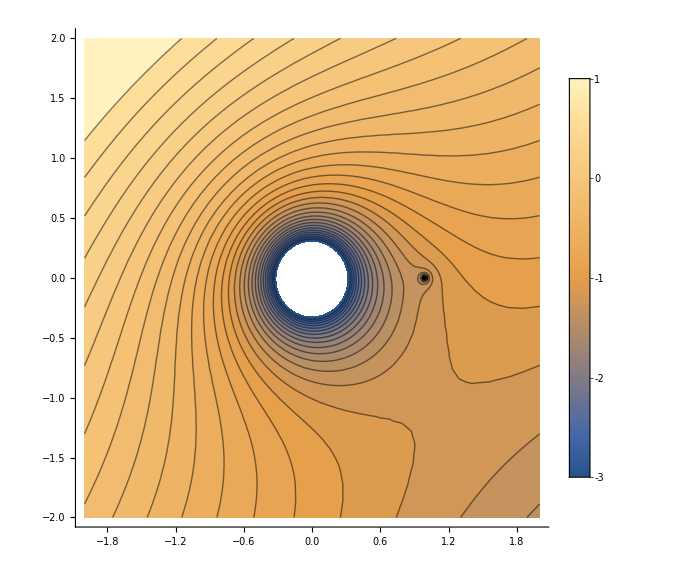

```mathematica
lim=2
ContourPlot[(H/.rules),{x,-lim,lim},{y,-lim,lim},
Axes->True,
Frame->False,
PlotLegends->Automatic,
Contours->30,
ImageSize->Large]
```

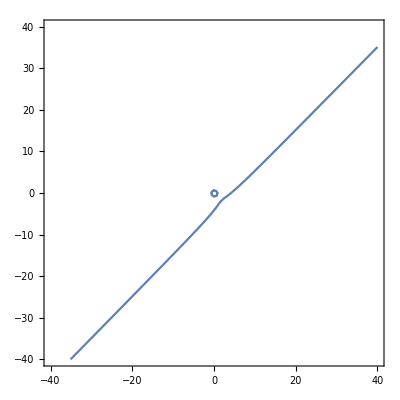

```mathematica
ContourPlot[(H/.rules)==-1.4,{x,-20lim,20lim},{y,-20lim,20lim}]
```